# Eigenstates of a Josephson Junction

According to Eq. (8.56) the Hamiltonian of a Josephson Junction (JJ) is given by the expression

where the quantum operators Q, Φ obey the commutation relation [Φ,Q]=-i ℏ, or [Φ/Φ_0,Q/e]=-i ,

If the eigenvalues of Φ/Φ_0 are represented by the dimensionless continuous parameter θ, the above commutation relations suggests that

Inserting these relations into the Hamiltonian, we get

and the Schrodinger energy eigenvalue equation becomes

where γ≡E_J/E_C, and ϵ = E/ E_c .

This is the standard form of a 1D Schrodinger equation for a particle in a potential field given by

```mathematica
ClearAll["Global`*"];
v[θ_,γ_]=γ(1-Cos[θ]);
```

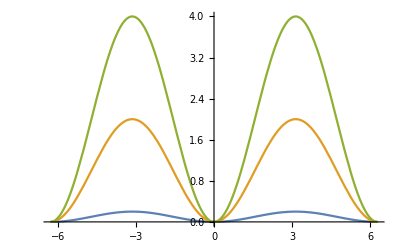

```mathematica
(* we plot the respective potential functions v[θ,γ] for the values γ=0.1, 1, 2 *)
Plot[{v[θ,0.1],v[θ,1],v[θ,2]},{θ,-2Pi,2Pi}]
```

The potential is periodic in θ and the trapping (the concave segment in the figure) region becomes more constrained as the parameter γ gets larger.

The  differential equation can be re-cast into a more familiar, or canonical, form called the Mathieu equation.
First we re-write Eq. (1)

where y(θ)≡ ψ(2θ), a=ϵ-γ, q ≡ -γ/2

The solutions of the second equation, called the Mathieu equation, are the Mathieu functions. In Mathematica they are represented by the commands MathieuS(a,q,y)  and MathieuC(a,q,y). Let’s plot these functions, for a potential that we associate with parameter γ = 2 or q=-1.

```mathematica
equation=-4  ψ''[θ]+ v[θ,γ]ψ[θ]- eig ψ[θ]==0
```

-eig ψ[θ]+γ (1-Cos[θ]) ψ[θ]-4 ψ''[θ]==0

```mathematica
rule=Flatten[DSolve[equation,ψ[θ],θ]] /. {C[1]->c1,C[2]->c2}
```

{ψ[θ]→c1 MathieuC[eig-γ,-γ/2,θ/2]+c2 MathieuS[eig-γ,-γ/2,θ/2]}

```mathematica
wave[θ_,c1_,c2_,γ_,eig_]:=c1 N[MathieuC[eig-γ,-γ/2,θ/2]]+c2 N[MathieuS[eig-γ,-γ/2,θ/2]]
```

I am going to arbitrarily choose c1=1, c2=0, and for γ=2,  in order to to “guess” an eigenvalue eig=0.3.

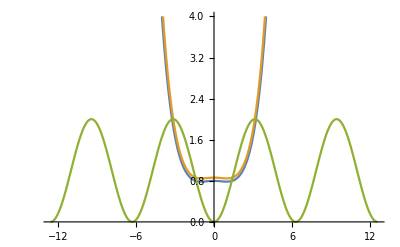

```mathematica
c1=1;c2=0;γ=2;eig=0.3;
Plot[{Re[wave[θ,1,0,2,0.3]],Im[wave[θ,1,0,2,0.3]],v[θ,1]},{θ,-4Pi,4Pi},PlotRange->{0,4}]
Clear[c1,c2,γ,eig];
```

In this figure the green line represents the background potential and the blue, orange lines the real and imaginary parts of the solution. Notice that the real part (blue line) and imaginary parts (orange line) exhibit unbounded exponential behavior. Because the wavefunction must be a bounded periodic function, this particular solution is unphysical and must be discarded. 
In other words, we chose a bad value for the eigenvalue for the parameter a,  which is related to the energy eigenvalue 
a=ϵ -  γ
We need to adjust our value for a so that the solutions possess well behaved periodic properties. These eigenvalues are called characteristic values of the corresponding Mathieu function.

For the even parity Mathieu ( MathieuC)  functions we use the following

```mathematica
?MathieuC
?MathieuCharacteristicA
?MathieuCharacteristicExponent
```

RowBox[{"MathieuC", "[", RowBox[{StyleBox["a", "TI"], ",", StyleBox["q", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the even Mathieu function with characteristic value StyleBox["a", "TI"] and parameter StyleBox["q", "TI"].

RowBox[{"MathieuCharacteristicA", "[", RowBox[{StyleBox["r", "TI"], ",", StyleBox["q", "TI"]}], "]"}] gives the characteristic value SubscriptBox[StyleBox["a", "TI"], StyleBox["r", "TI"]] for even Mathieu functions with characteristic exponent StyleBox["r", "TI"] and parameter StyleBox["q", "TI"].

RowBox[{"MathieuCharacteristicExponent", "[", RowBox[{StyleBox["a", "TI"], ",", StyleBox["q", "TI"]}], "]"}] gives the characteristic exponent StyleBox["r", "TI"] for Mathieu functions with characteristic value StyleBox["a", "TI"] and parameter StyleBox["q", "TI"].

see also

```mathematica
URL["http://mathworld.wolfram.com/MathieuFunction.html"]
```

URL[http://mathworld.wolfram.com/MathieuFunction.html]

In order to "guess" the correct values for parameter a we use the fact that any solution of Mathieu's equation has the form
e^(i r θ) u(θ)
where the parameter r is called the characteristic exponent, and u(θ) is a period function of θ, with period π (this is called Floquet’s theorem). It is clear that periodic unbounded solutions exist only if the imaginary part of the exponent r vanishes. Let’s investigate the structure of this exponent by using the Mathematica function MathieuCharacteristicExponent[a,q], and tagging those regions in which the imaginary part of the exponent vanishes (shown by the red line along the horizontal axis).

```mathematica
Manipulate[Plot[Im[MathieuCharacteristicExponent[a,-γ/2 ]],{a,a1,a2},PlotStyle->Red,PlotRange->{-0.1,0}],{{a1,-10},-10,10},{{a2,10},-10,10},{γ,{0,1.0,2.0,3.0}},SaveDefinitions->True]
```

In the figure, we note that for γ=0, the characteristic exponents with vanishing imaginary parts lie on the positive a-axis, but for γ=1, the regions in which Im(r)=0 constitute “islands”, or bands,  on the horizontal axis. Closer inspection shows that the first, left-most band, lies, roughly, in the region where -0.11 < a < 0.45.  Let’s plot our solution for choices of  a in this interval.

```mathematica
evenwave[γ_,a_]:=Plot[{Re[wave[θ,1,0,γ,γ+a]],v[θ,γ]} ,{θ,-10Pi,10Pi},PlotRange->{-2,2}]
```

```mathematica
Manipulate[evenwave[1,a],{a,-0.1,0.45},SaveDefinitions->True]
```

Note that the wavefunction is well behaved, and periodic, for all values of a in that interval. However the probability amplitude is un-localized. A first principles derivation of the Josephson equations demands that we impose additional boundary conditions so that 
ψ(θ)=ψ(θ+2 n π)  n=±1,2, ...
In that case we require that the characteristics exponent has vales r=0,±2,±4 ... . The values of the a parameters associated with these exponents can be obtained using the Mathematica function MathieuCharacteristicA[r,q], and are labeled a_r

```mathematica
ar[r_,γ_]:=N[MathieuCharacteristicA[r,-γ/2]]
Table[ar[r,1],{r,0,4,2}]
```

{-0.121766,4.1009,16.0084}

You may note that these values lie in the “island” regions, or energy bands,  discussed above.

```mathematica
eveneig[r_,γ_]=N[γ+ar[r,γ]];
geven[r_,γ_]:=Plot[{Re[wave[θ,1,0,γ,eveneig[r,γ]]],Im[wave[θ,1,0,γ,eveneig[r,γ]]],v[θ,γ]},{θ,-Pi,Pi},PlotRange->All]
```

Let’s plot these wavefunctions for γ=2, and r=2,4,6

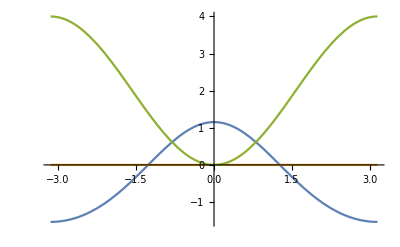

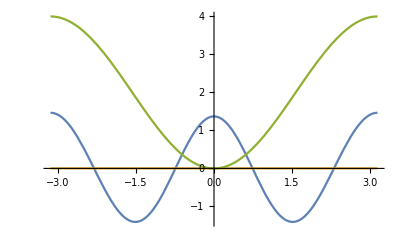

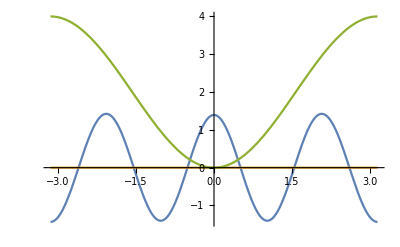

```mathematica
geven[2,2]
geven[4,2]
geven[6,2]
```

Note that the corresponding wavefunction (the blue real part) does indeed satisfy the periodicity requirement.

A similar analysis applies to the odd  Mathieu functions. In that case we use MathieuCharacteristicB[r,q] to find the characteristic values b_r

```mathematica
br[r_,γ_]:=N[MathieuCharacteristicB[r,-γ/2]]
Table[br[r,1],{r,1,4,2}]
```

{1.46677,9.01761}

```mathematica
oddeig[r_,γ_]=N[γ+ar[r,γ]];
```

```mathematica
godd[r_,γ_]:=Plot[{Re[wave[θ,0,1,γ,oddeig[r,γ]]],Im[wave[θ,0,1,γ,oddeig[r,γ]]],v[θ,γ]},{θ,-2Pi,2Pi}]
```

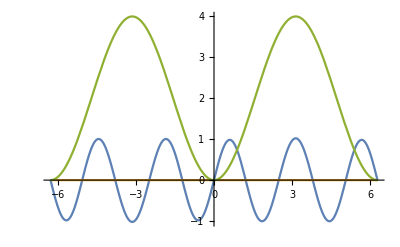

```mathematica
(* below we plot the wavefunction for r=5 *)
godd[5,2]
```

## Comparison with SHO eigenstates

In the text, we pointed out that for small oscillations around θ=0, we can replace H_JJ with that of a harmonic oscillator.

```mathematica
eveneig[r_,γ_]=N[γ+ar[r,γ]];
```

```mathematica
oddeig[r_,γ_]=N[γ+br[r,γ]];
```

```mathematica
eigtable[γ_]:=Flatten[Table[{eveneig[r,γ],oddeig[r+1,γ]},{r,0,4,2}]]
SHO[γ_]:=Table[√γ(2n+1)-(3 n^2+4 n+3)/12,{n,0,4}]
```

```mathematica
eigplot[γ_]:=ListPlot[{eigtable[γ],SHO[γ]},PlotRange->All]
```

In the Table below we compare the exact eigenvalues with the SHO eigenvalues for various values of γ

```mathematica
Manipulate[eigplot[γ],{γ,1,100},SaveDefinitions->True]
```

```mathematica
DeltaEplot[γ_]:=ListPlot[{Differences[eigtable[γ]],Differences[SHO[γ]]},PlotRange->All]
```

Below we compare the difference between the exact and SHO eigenvalues for various γ

```mathematica
Manipulate[DeltaEplot[γ],{γ,1,100},SaveDefinitions->True]
```